CreateDirectory::filex: "C:\\Users\\Petr\\Desktop\\Projects\\Programming Techniques\\shown results\\" already exists.

CreateDirectory::filex: "C:\\Users\\Petr\\Desktop\\Projects\\Programming Techniques\\shown results\\search\\" already exists.

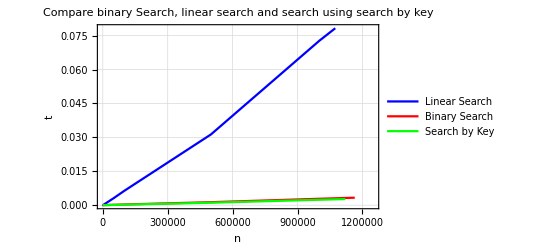

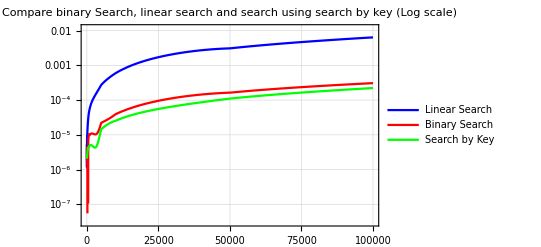

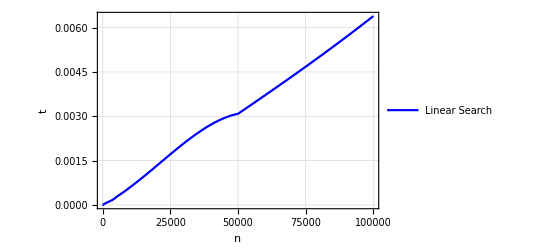

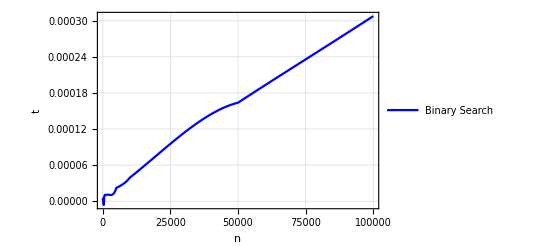

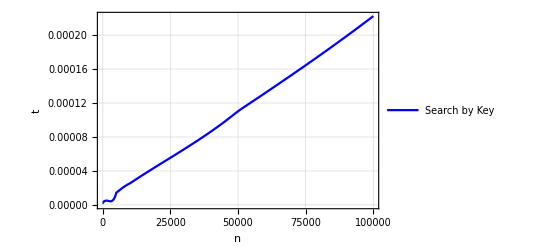

```mathematica
SetDirectory[NotebookDirectory[]];
workingDirectory = CreateDirectory["shown results"];
SetDirectory[workingDirectory];
file= OpenRead["../log_search.txt"];
workingDirectory = CreateDirectory["search"];
SetDirectory[workingDirectory];
filelist= ReadList[file,String];

mapSearchResults = filelist[[3;;;;4]];
binarySearchResults = filelist[[2;;;;4]];
linearSearchResults = filelist[[1;;;;4]];
linearSearchResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,linearSearchResults];
binarySearchResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,binarySearchResults];
mapSearchResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,mapSearchResults];
linearSearchResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,linearSearchResults];
binarySearchResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,binarySearchResults];
mapSearchResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,mapSearchResults];
Plot1 = Show[ListPlot[linearSearchResults,Joined->True,PlotStyle->Blue,PlotLegends->{"Linear Search"},PlotLabel->"Compare binary Search, linear search and search using search by key", AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]],ListPlot[binarySearchResults,Joined->True,PlotStyle->Red,PlotLegends->{"Binary Search"}],
ListPlot[mapSearchResults,Joined->True,PlotStyle->Green,PlotLegends->{"Search by Key"}]]
linearFunc = Interpolation[linearSearchResults];
binaryFunc = Interpolation[binarySearchResults];
mapFunc = Interpolation[mapSearchResults];
Plot2 = LogPlot[{linearFunc[x],binaryFunc[x], mapFunc[x]},{x,0,10^5},PlotStyle->{Blue,Red, Green},PlotLegends->{"Linear Search","Binary Search","Search by Key"},PlotLabel->"Compare binary Search, linear search and search using search by key (Log scale)",PlotTheme->"Detailed",ImageSize->Scaled[0.8]]
Plot3 = Plot[linearFunc[x],{x,0,10^5},PlotStyle->Blue,PlotLegends->{"Linear Search"},AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]]
Plot4 = Plot[binaryFunc[x],{x,0,10^5},PlotStyle->Blue,PlotLegends->{"Binary Search"},AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]]
Plot5 = Plot[mapFunc[x],{x,0,10^5},PlotStyle->Blue,PlotLegends->{"Search by Key"},AxesLabel->{"n","t"},PlotTheme->"Detailed",ImageSize->Scaled[0.8]]
```

```mathematica
Export["Comp1.gif",Plot1,ImageSize->2048];
Export["Comp2.gif",Plot2,ImageSize->2048];
Export["Linear.gif",Plot3,ImageSize->2048];
Export["Binary.gif",Plot4,ImageSize->2048];
Export["Map.gif",Plot5,ImageSize->2048];
```

```mathematica
grid = Grid[Transpose[{Join[{"Time"},binarySearchResults[[All,1]]],Join[{"Linear Search"},linearSearchResults[[All,2]]],Join[{"Binary Search"},binarySearchResults[[All,2]]],Join[{"Search by Key"},mapSearchResults[[All,2]]]}],Frame->All,Alignment->Left,Background->{None,{Yellow}},ItemStyle->Directive[FontSize->20,Bold]]
```

Time | Linear Search | Binary Search | Search by Key
5 | 3.44568×10^-6 | 2.24335×10^-6 | 2.19204×10^-6
10 | 2.10406×10^-6 | 2.58792×10^-6 | 2.16271×10^-6
50 | 4.34375×10^-6 | 4.20446×10^-6 | 2.302×10^-6
100 | 7.18094×10^-6 | 4.07616×10^-6 | 2.54394×10^-6
500 | 0.0000310184 | 7.44486×10^-6 | 4.0615×10^-6
1000 | 0.0000567254 | 9.87149×10^-6 | 4.95224×10^-6
5000 | 0.000272087 | 0.000022056 | 0.0000143472
10000 | 0.000591659 | 0.0000390974 | 0.000025344
50000 | 0.00308389 | 0.000163809 | 0.000110463
100000 | 0.0063882 | 0.000307699 | 0.000222297
500000 | 0.0313082 | 0.00132553 | 0.00108427
1000000 | 0.0726869 | 0.0028336 | 0.00240398
5000000 | 0.373387 | 0.0143812 | 0.0124827

```mathematica
Export["TableSerch.gif",grid,ImageSize->{2048,720}];
Export["TableSeach.xls",grid,ImageSize->{2048,720}];
```